## Working with Quantum Circuits

We will now review the common procedure for working with quantum circuits in the Wolfram Quantum Framework. This will help you develop a stronger understanding of the foundations of quantum computation, in particular, how to think in terms of quantum objects, the information they contain, and the ways they operate.

## Key Concepts

Quantum circuit

Quantum operators

Quantum gates

## Specifying Circuits

You have already seen several examples using the Wolfram Quantum Framework. Let’s pause for a moment to learn more about it explicitly. Many of the tricks and details we will cover are useful for quantum computation in general, regardless of the platform you use for simulation.

The framework provides a convenient shorthand notation for building circuits. Most quantum gates and states are referred to by their common names, and these same names are adopted in the Wolfram Quantum Framework as well.

For example, consider the following circuit:

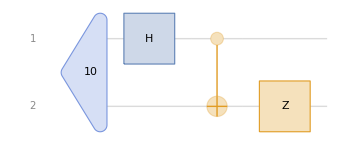

```mathematica
QuantumCircuitOperator[{"10","H","CNOT","Z"->2}]["Diagram"]
```

This shorthand represents a two-qubit input state 10, followed by a Hadamard gate (denoted 𝐻) acting on the first qubit, a CNOT gate with the first qubit as control and the second qubit as target, and finally a Pauli-Z gate (denoted 𝑍) acting on the second qubit.

When thinking about gates, focus on two things: what the gate is (usually one of the common named gates) and where it acts (on which qubits or wires). In the Wolfram Quantum Framework, if no target qubits are specified, the framework uses default conventions. For example, in the circuit above, the Hadamard gate 𝐻 acts on the first qubit, while the CNOT gate acts on qubits {1,2}, with the first qubit as control and the second as target. Compare that circuit and its gate placements with the one shown below:

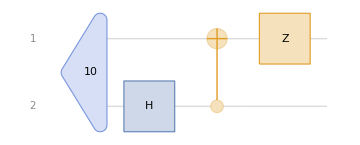

```mathematica
QuantumCircuitOperator[{"10","H"->2,"CNOT"->{2,1},"Z"}]["Diagram"]
```

In many textbooks, when an initial state other than the register state is required, authors prefer to create that state using gates. For example, the state 10 can be prepared by applying a NOT gate (or X gate) to the first qubit of the two-qubit register state 00.

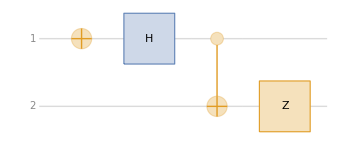

```mathematica
QuantumCircuitOperator[{"NOT","H","CNOT","Z"->2}]["Diagram"]
```

The circuit above has no measurement operators. Therefore, evaluating the circuit produces a quantum state:

```mathematica
QuantumCircuitOperator[{"NOT","H","CNOT","Z"->2}][]
```

QuantumState[…]

As you can see, we did not provide any input when executing the circuit above. By default, the circuit starts with the register state. If you want to use a specific initial state instead, you can supply it as input, as shown below:

```mathematica
QuantumCircuitOperator[{"NOT","H","CNOT","Z"->2}][QuantumState[{α,β}]]
```

QuantumState[…]

The traditional form of the above quantum object (which is a quantum state) will return the state in the Dirac notation:

```mathematica
QuantumCircuitOperator[{"NOT","H","CNOT","Z"->2}][QuantumState[{α,β}]]//TraditionalForm
```

(α/(√2)+β/(√2))00+(α/(√2)-β/(√2))11

You can build up larger quantum circuits by nesting QuantumCircuitOperator objects. The second argument can be used to label sub-circuits:

```mathematica
qc=QuantumCircuitOperator[{
QuantumCircuitOperator[{"RY"[π/3],"RY"[π/6]->2,"RY"[π/7]->3},"First Part"],
QuantumCircuitOperator[{"CZ","CZ"->{1,3},"CZ"->{1,4},"CZ"->{2,3},"CZ"->{3,4}},"Second Part"],
Range[4]
}]
```

This can be helpful if you want to label various parts of an algorithm’s diagram:

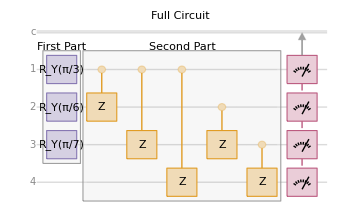

```mathematica
qc["Diagram",PlotLabel->"Full Circuit"]
```

Additionally, a circuit can be built by composing smaller circuits together. For example:

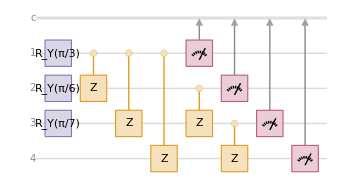

```mathematica
qi=QuantumCircuitOperator[{"RY"[π/3],"RY"[π/6]->2,"RY"[π/7]->3}];
qii=QuantumCircuitOperator[{"CZ","CZ"->{1,3},"CZ"->{1,4},"CZ"->{2,3},"CZ"->{3,4}}];
qiii=QuantumCircuitOperator[{{1},{2},{3},{4}}];
qc2=qi/*qii/*qiii;
qc2["Diagram"]
```

Check that two circuits are the same

```mathematica
qc==qc2
```

True

When a circuit contains measurement, evaluating it produces a quantum measurement object:

```mathematica
meas=qc[]
```

QuantumMeasurement[…]

The measurement object can provide a variety of useful information, such as the probability distribution over possible outcomes or the actual measurement results.

Return all probabilities:

```mathematica
FullSimplify/@meas["Probabilities"]
```

<|0000→3/32 (2+√3) (1+Cos[π/7]),0001→0,0010→3/16 (2+√3) Sin[π/14]^2,0011→0,0100→-3/32 (-2+√3) (1+Cos[π/7]),0101→0,0110→3/32 (-2+√3) (-1+Cos[π/7]),0111→0,1000→1/32 (2+√3) (1+Cos[π/7]),1001→0,1010→1/16 (2+√3) Sin[π/14]^2,1011→0,1100→-1/32 (-2+√3) (1+Cos[π/7]),1101→0,1110→1/32 (-2+√3) (-1+Cos[π/7]),1111→0|>

Plot the corresponding probabilities:

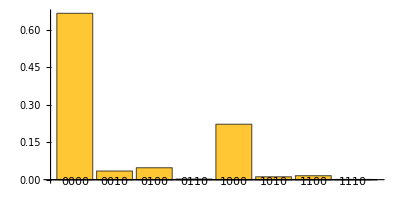

```mathematica
meas["ProbabilityPlot",AspectRatio->1/2]
```

You can also use the measurement object to simulate measurement results, mimicking the outcomes of repeated runs of an actual experiment:

Simulate 1240 runs of measurement using the quantum measurement object:

```mathematica
mea1["SimulatedMeasurement",1240]//Counts
```

<|0000→829,1000→265,0100→61,0010→47,1100→19,0110→3,1010→15,1110→1|>

Note that the Wolfram Quantum Framework returns the exact probabilities dictated by the laws of quantum theory. It does not compute frequencies from repeated sampling.

Return non-zero probabilities:

```mathematica
FullSimplify/@meas["Probability"]
```

<|0000→3/32 (2+√3) (1+Cos[π/7]),0010→3/16 (2+√3) Sin[π/14]^2,0100→-3/32 (-2+√3) (1+Cos[π/7]),0110→3/32 (-2+√3) (-1+Cos[π/7]),1000→1/32 (2+√3) (1+Cos[π/7]),1010→1/16 (2+√3) Sin[π/14]^2,1100→-1/32 (-2+√3) (1+Cos[π/7]),1110→1/32 (-2+√3) (-1+Cos[π/7])|>

Return numerical values:

```mathematica
N@meas["Probability"]
```

<|0000→0.665111,0010→0.034649,0100→0.0477528,0110→0.00248769,1000→0.221704,1010→0.0115497,1100→0.0159176,1110→0.000829228|>

## Equivalent Operators and Circuits

Given the measurement distribution in the last example, you might suspect that a simpler circuit could achieve the same results. This is often the case when designing quantum algorithms. One of the key engineering challenges in practical quantum computing is creating circuits with few enough gates to run effectively.

This has a couple of advantages:

On actual quantum hardware, adding more gates increases the noise in the system, which degrades the outcomes and makes them less reliable.

For classical simulation, fewer gates usually mean lower computational costs.

Consider the following circuits, which are different implementations of the Toffoli gate. The simplest form of the Toffoli gate—though nontrivial to implement directly in hardware—is a controlled gate with two control qubits and one target qubit. As you can see, it flips the third qubit only when the first two qubits are both 1.

```mathematica
toffoli1=QuantumCircuitOperator[{QuantumOperator["Toffoli"]}];
```

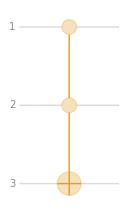
-Graphics-  ψ | Toffoliψ
000 | 000
001 | 001
010 | 010
011 | 011
100 | 100
101 | 101
110 | 111
111 | 110

```mathematica
Row[{toffoli1["Diagram"],"  ",TableForm[{TraditionalForm[#],TraditionalForm[toffoli1[#]]}&/@QuantumBasis[2,3]["BasisStates"],TableHeadings->{None, {"ψ","Toffoliψ"}}]}]
```

Another representation of Toffoli gate is as follow:

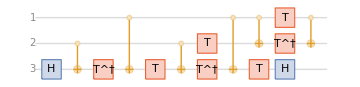

```mathematica
toffoli2=QuantumCircuitOperator["Toffoli"];
toffoli2["Diagram"]
```

The T gate is a single-qubit quantum gate, also called the π/8 gate (because it represents a rotation of π/4 around the Z axis).

Another implementation of Toffoli gate is using the square root of X gate

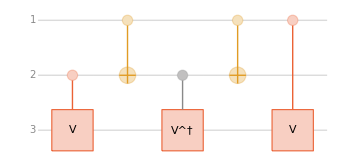

```mathematica
toffoli3=QuantumCircuitOperator[{"C"["SX"]->{2,3},"CNOT","C"[QuantumOperator["SX"]["Dagger"]]->{2,3},"CNOT","C"["SX"]->{1,3}}];
toffoli3["Diagram"]
```

Note in the Wolfram quantum framework, one can apply usual algebraic operations on operators too:

```mathematica
QuantumOperator["SX"]==√QuantumOperator["X"]
```

True

Calculate depth of these circuits:

```mathematica
#["Depth"]&/@{toffoli1,toffoli2,toffoli3}
```

{1,11,5}

Check that the overall effect of all three circuits is the same, even though they are constructed differently. In other words, each circuit implements the Toffoli gate (and, depending on the decomposition, may be equivalent up to a global phase). You can verify this by comparing their action on all computational-basis inputs—or by confirming that their unitaries are identical.

```mathematica
toffoli1["CircuitOperator"]==toffoli2["CircuitOperator"]==toffoli3["CircuitOperator"]
```

True

## Pauli Operators

You might have noticed that an X gate seems to act a lot like a NOT gate. That’s because they have identical effects on qubits. An X gate is a NOT gate.

```mathematica
QuantumOperator["X"]==QuantumOperator["NOT"]
```

True

Recall the Bloch sphere representation of a qubit:

```mathematica
GraphicsGrid[Apply[
QuantumState[#2]["BlochPlot",PlotLabel->Highlighted[QuantumState[QuantumState[#2],#1],Background->LightOrange]]&,{{{"Z","Up"},{"Z","Down"}},{{"X","+"},{"X","-"}},{{"Y","R"},{"Y","L"}}},{2}],Frame->All]
```

-Graphics-

Each of the six states shown above lie along the Cartesian axes of the sphere. For various historical reasons, these states have alternate names in the context of quantum computing. However, they have another interpretation in the context of linear algebra. They simply correspond to eigenvectors of the Pauli matrices:

```mathematica
Table[PauliMatrix[k]//MatrixForm,{k,3}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

```mathematica
Table[QuantumOperator[k]["Matrix"]//MatrixForm,{k,{"X","Y","Z"}}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

A future lesson will discuss the matrix representation of quantum states in more detail.

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]